```mathematica
x4p= Import["/Users/ashutosh/LCX_analysis/X1_4_X2_Mu_X_0.077"];
```

```mathematica
x4m= Import["/Users/ashutosh/LCX_analysis/X1_4_X2_Mu_X_-0.077"];
```

```mathematica
y4p= Import["/Users/ashutosh/LCX_analysis/X1_4_X2_Mu_Y_0.077"];
```

```mathematica
y4m= Import["/Users/ashutosh/LCX_analysis/X1_4_X2_Mu_Y_-0.077"];
```

```mathematica
z4p= Import["/Users/ashutosh/LCX_analysis/X1_4_X2_Mu_Z_0.077"];
```

```mathematica
z4m= Import["/Users/ashutosh/LCX_analysis/X1_4_X2_Mu_Z_-0.077"];
```

```mathematica
x19p= Import["/Users/ashutosh/LCX_analysis/X1_19_X2_Mu_X_0.077"];
```

```mathematica
x19m= Import["/Users/ashutosh/LCX_analysis/X1_19_X2_Mu_X_-0.077"];
```

```mathematica
y19p= Import["/Users/ashutosh/LCX_analysis/X1_19_X2_Mu_Y_0.077"];
```

```mathematica
y19m= Import["/Users/ashutosh/LCX_analysis/X1_19_X2_Mu_Y_-0.077"];
```

```mathematica
z19p= Import["/Users/ashutosh/LCX_analysis/X1_19_X2_Mu_Z_0.077"];
```

```mathematica
z19m= Import["/Users/ashutosh/LCX_analysis/X1_19_X2_Mu_Z_-0.077"];
```

```mathematica
diffxp = x19p - x4p ;
```

```mathematica
f[i_,j_] := If[Abs[diffxp[[i,j]]]  > 0.005, diffxp[[i,j]] ,0 ];
```

```mathematica
diffxpm = Table[f[i,j],{i,55},{j,9}];
```

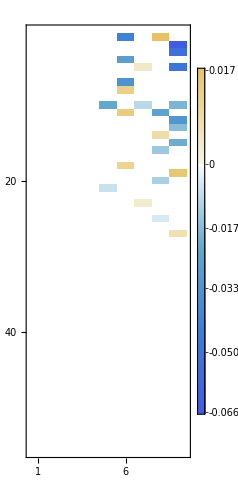

```mathematica
MatrixPlot[%186,PlotTheme->"Detailed"]
```

```mathematica
diffxpm //MatrixForm
```

(0 | 0 | 0 | 0 | 0 | -0.0337739 | 0 | 0.0172674 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0665829
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.046714
0 | 0 | 0 | 0 | 0 | -0.0147033 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.00527251 | 0 | -0.0429393
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.0200124 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0146318 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.012784 | 0 | -0.00701143 | 0 | -0.0113462
0 | 0 | 0 | 0 | 0 | 0.0155076 | 0 | -0.0138549 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0194526
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0111614
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0091489 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0125852
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00847985 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.013865 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0161767
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0077097 | 0
0 | 0 | 0 | 0 | -0.00606251 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.00504229 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00551877 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00876686
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
g[i_,j_] := If[Abs[diffxp[[i,j]]]  > 0.001, Abs[x19p[[i,j]]]-  Abs[x4p[[i,j]]],0 ];
```

```mathematica
diffxpmg = Table[g[i,j],{i,55},{j,9}]
```

{{0,0,0,0,0,-0.0337739,0,-0.0172674,0},{0,0,0,0,-0.00394803,0,-0.0026873,0,-0.0665829},{0,0,-0.00202699,0,0,0,-0.00448073,0,-0.046714},{0,0,0,0,0,-0.0147033,0,0,0},{0,0,0,0,-0.0048411,0,-0.00527251,0,-0.0429393},{0,0,0,0,-0.0017789,0,-0.00492311,0,0.00120718},{0,0,0,0,0,-0.0200124,0,-0.00361783,0},{0,0,0,-0.00130915,0,-0.0146318,0,0,0},{0,0,0,-0.00240998,0,-0.00441978,0,-0.00113917,0},{0,0,0,0,-0.012784,0,-0.00701143,0,-0.0113462},{0,0,0,0,0,-0.0155076,0,-0.0138549,0},{0,0,-0.00170329,0,0,0,0.00211042,0,0.0194526},{0,0,0,0,-0.00372609,0,0,0,-0.0111614},{0,0,0,0,0,-0.00489334,0,-0.0091489,0},{0,0,0,0,0,0,0,0,-0.0125852},{0,0,0,-0.00130372,0,-0.00337579,0,-0.00847985,0},{0,0,0,0,0,0,-0.00301721,0,0},{0,0,0,0,0,-0.013865,0,-0.00429361,0},{0,0,0,0,-0.00398983,0,0,0,-0.0161767},{0,0,0,0,0,0,0,-0.0077097,0},{0,0,0,0,-0.00606251,0,-0.00228162,0,0},{0,0,0,0,0,-0.0042579,0,0,0},{0,0,0,0,0,0,-0.00504229,0,-0.0032511},{0,0,0,0,0,-0.0013629,0,-0.00188894,0},{0,0,0,0,0,-0.00403925,0,-0.00551877,0},{0,0,0,0,-0.00215034,0,-0.00159476,0,-0.00132073},{0,0,0,0,-0.00158779,0,0,0,-0.00876686},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-0.00361846},{0,0,0,0,0,0,0,0,0},{0,0,0,0,-0.00147732,0,0,0,0},{0,0,0,0,-0.00142449,0,-0.0010594,0,-0.00180246},{0,0,0,0,0,-0.00118767,0,0,0},{0,0,0,0,0,0,0,0,-0.00192158},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-0.00145289,0,-0.00111841,0},{0,0,0,0,0,0,0,0,-0.00104532},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-0.00111858},{0,0,0,0,0,-0.00126455,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-0.00112625},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

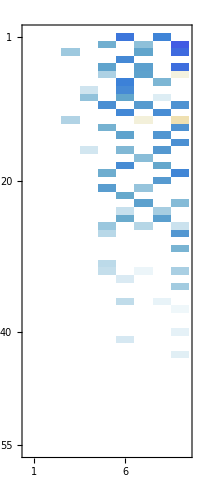

```mathematica
MatrixPlot[diffxpmg]
```

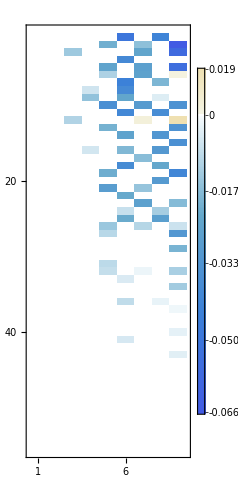

```mathematica
MatrixPlot[diffxpmg,PlotTheme->"Detailed"]
```